#### Problem 3 HW 11

```mathematica
k=1.381*10^(-23);
mO2=5.3134*10^(-26);
mN2=4.6518*10^(-26);
mH2=3.348*10^(-27)
```

3.348×10^-27

Part A

```mathematica
Dmb[v_,m_,T_]:=((m/(2*Pi*k*T))^(3/2))*4*Pi*(v^2)*Exp[-(m*(v^2))/(2*k*T)]
```

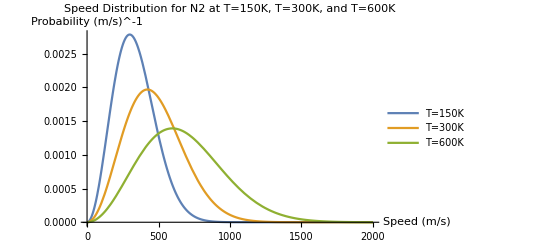

```mathematica
Plot[{Dmb[v,mN2,150],Dmb[v,mN2,300],Dmb[v,mN2,600]},{v,0,2000},PlotLabel->"Speed Distribution for N2 at T=150K, T=300K, and T=600K",PlotLegends-> {"T=150K","T=300K","T=600K"},AxesLabel->{"Speed (m/s)","Probability (m/s)^-1"}]
```

Part B

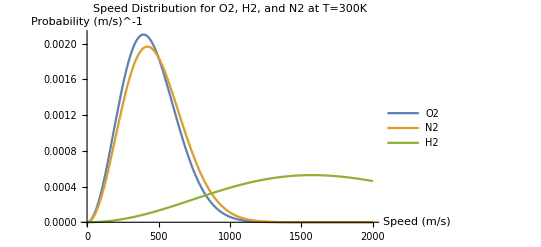

```mathematica
Plot[{Dmb[v,mO2,300],Dmb[v,mN2,300],Dmb[v,mH2,300]},{v,0,2000},PlotLabel->"Speed Distribution for O2, H2, and N2 at T=300K",PlotLegends-> {"O2","N2","H2"},AxesLabel->{"Speed (m/s)","Probability (m/s)^-1"}]
```

#### Problem 4b

Probability that Hydrogen molecules in Earth’s exobase will have a velocity greater than v_esc for Earth:

```mathematica
N[Integrate[Dmb[v,mH2,1000],{v,11185.7,100000}]]
```

1.17435×10^-6

Probability that Hydrogen molecules in Jupiter’s exobase will have a velocity greater than v_esc for Jupiter:

```mathematica
NIntegrate[Dmb[v, mH2, 1000],{v,60198.2,1000000}]
```

4.00855×10^-190

#### Problem 6

```mathematica
B=(300*8.617*10^-5)^-1
```

38.6832

```mathematica
P1[n_]:=Exp[-n*B]*(1-Exp[-1*B]);
P2[n_]:=Exp[-n*0.1*B]*(1-Exp[-0.1*B]);
P3[n_]:=Exp[-n*0.001*B]*(1-Exp[-0.001*B])
```

```mathematica
P1[0]
```

1.

```mathematica
P2[0]
```

0.979107

```mathematica
P3[0]
```

0.0379446

```mathematica
P1[1]
```

1.58522×10^-17

```mathematica
P2[1]
```

0.0204569

```mathematica
P3[1]
```

0.0365048

```mathematica
P1[2]
```

2.51292×10^-34

```mathematica
P2[2]
```

0.000427413

```mathematica
P3[2]
```

0.0351196

```mathematica
P1[3]
```

3.98354×10^-51

```mathematica
P2[3]
```

8.93011×10^-6

```mathematica
P3[3]
```

0.033787

```mathematica
N0[n_]:=(Exp[n*B]-1)^-1
```

```mathematica
N0[1]
```

1.58522×10^-17

```mathematica
N0[.1]
```

0.0213392

```mathematica
N0[0.001]
```

25.3542

#### Peer Problem

```mathematica
B=0.63;
kev=8.617*10^-5;
Tpp=300;
mu=1.03*10^-7;
alpha=(mu*B)/(kev*Tpp)
```

2.51015×10^-6

```mathematica
bo[j_]:=Exp[-j*alpha]
```

```mathematica
bo[-3/2]/(bo[-3/2]+bo[-1/2]+bo[1/2]+bo[3/2])
```

0.250001

```mathematica
bo[-3/2]
```

1.